# Incenter

### Author

Eric W. Weisstein
March 5, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneGeometry/Incenter.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Incenter.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

## Angle Bisctors

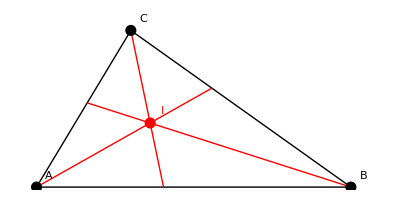

```mathematica
t=Triangle[{{0,0},{1,0},{.3,.5}}];
Show[Graphics[{
t,
{Red,AngleBisectors[t]},
PointLabels[Join[
Transpose[{VertexPoints[t],{"A","B","C"}}],
{{Incenter[t],"I",Red}}
],LabelOffset->.04]
}],AspectRatio->Automatic,PlotRange->All]
```

## Manipulate

```mathematica
Incenter[p1:{x1_,y1_},p2:{x2_,y2_},p3:{x3_,y3_}]:=Module[{a=Norm[p2-p3],b=Norm[p3-p1],c=Norm[p1-p2]},
Point[Transpose[{p1,p2,p3}].{a,b,c}/(a+b+c)]
]

Incircle[p1:{x1_,y1_},p2:{x2_,y2_},p3:{x3_,y3_}]:=Module[{a=Norm[p2-p3],b=Norm[p3-p1],c=Norm[p1-p2],center,radius},
(*center={a x1+b x2+c x3,a y1+b y2+c y3}/(a+b+c);*)
center=Transpose[{p1,p2,p3}].{a,b,c}/(a+b+c);
radius=Sqrt[(b+c-a)(c+a-b)(a+b-c)/(a+b+c)]/2;
Circle[center,radius]
]
```

```mathematica
Manipulate[Graphics[{
{Red,Incircle[p1,p2,p3],PointSize[.02],Incenter[p1,p2,p3]},
Line[{p1,p2,p3,p1}]},
PlotRange->1.5],{{p1,{0,0}},{-1,-1},{1,1},ControlType->Locator},{{p2,{1,0}},{-1,-1},{1,1},ControlType->Locator},{{p3,{0,1}},{-1,-1},{1,1},ControlType->Locator}]
```

## Distances

### ICl

```mathematica
FullSimplify[ToSidelengths[Distance[Incenter,ClawsonPoint]^2],TriangleQ[]]
```

(4 a b c (-a^10-a^6 b^2 c^2+a^9 (b+c)-2 a^7 b c (b+c)+2 a^3 b^2 (b-c)^2 c^2 (b+c)+a^4 b (b-c)^2 c (b+c)^2+a^8 (b^2+c^2)-(b-c)^4 (b+c)^2 (b^2+c^2) (b^2+b c+c^2)+a^2 (b-c)^2 (b+c)^2 (b^4-2 b^3 c+b^2 c^2-2 b c^3+c^4)-a^5 (b+c) (2 b^4-3 b^3 c+b^2 c^2-3 b c^3+2 c^4)+a (b^9-2 b^7 c^2+b^5 c^4+b^4 c^5-2 b^2 c^7+c^9)))/((a+b+c) ((a-b)^2 (a+b) (a^2+b^2)-(a^2-b^2)^2 c+2 a b (a+b) c^2-(a+b) c^4+c^5)^2)

```mathematica
Factor[%]
```

-(4 a b c (a^10-a^9 b-a^8 b^2+2 a^5 b^5-a^2 b^8-a b^9+b^10-a^9 c+2 a^7 b^2 c-a^5 b^4 c-a^4 b^5 c+2 a^2 b^7 c-b^9 c-a^8 c^2+2 a^7 b c^2+a^6 b^2 c^2-2 a^5 b^3 c^2-2 a^3 b^5 c^2+a^2 b^6 c^2+2 a b^7 c^2-b^8 c^2-2 a^5 b^2 c^3+2 a^4 b^3 c^3+2 a^3 b^4 c^3-2 a^2 b^5 c^3-a^5 b c^4+2 a^3 b^3 c^4-a b^5 c^4+2 a^5 c^5-a^4 b c^5-2 a^3 b^2 c^5-2 a^2 b^3 c^5-a b^4 c^5+2 b^5 c^5+a^2 b^2 c^6+2 a^2 b c^7+2 a b^2 c^7-a^2 c^8-b^2 c^8-a c^9-b c^9+c^10))/((a+b+c) (a^5-a^4 b-a b^4+b^5-a^4 c+2 a^2 b^2 c-b^4 c+2 a^2 b c^2+2 a b^2 c^2-a c^4-b c^4+c^5)^2)

```mathematica
ToAngles[%]
```

-(4 a b c (-a^9 b+2 a^5 b^5-a b^9-a^9 c+2 a^7 b^2 c-a^5 b^4 c-a^4 b^5 c+2 a^2 b^7 c-b^9 c+2 a^7 b c^2-2 a^5 b^3 c^2-2 a^3 b^5 c^2+2 a b^7 c^2-2 a^5 b^2 c^3+2 a^4 b^3 c^3+2 a^3 b^4 c^3-2 a^2 b^5 c^3-a^5 b c^4+2 a^3 b^3 c^4-a b^5 c^4+2 a^5 c^5-a^4 b c^5-2 a^3 b^2 c^5-2 a^2 b^3 c^5-a b^4 c^5+2 b^5 c^5+2 a^2 b c^7+2 a b^2 c^7-a c^9-b c^9+16 Area^2 (a^2+b^2+c^2)^2 HK^2))/((a+b+c) (a^5-a^4 b-a b^4+b^5-a^4 c+2 a^2 b^2 c-b^4 c+2 a^2 b c^2+2 a b^2 c^2-a c^4-b c^4+c^5)^2)

### IF

```mathematica
FullSimplify[Together//@ToSidelengths[Distance[Incenter,FeuerbachPoint]^2/.Cos[x_]:>TrigExpand[Cos[x]]],TriangleQ[]]
```

-((a-b-c) (a+b-c) (a-b+c))/(4 (a+b+c))

```mathematica
ToAngles[%]
```

Inradius^2

### IG

```mathematica
FullSimplify[ToSidelengths[Distance[Incenter,Centroid]^2],TriangleQ[]]
```

1/9 (-a^2-15 a b-b^2+3 (a+b) c-c^2+(18 a b (a+b))/(a+b+c))

```mathematica
Factor[%]
```

-(a^3-2 a^2 b-2 a b^2+b^3-2 a^2 c+9 a b c-2 b^2 c-2 a c^2-2 b c^2+c^3)/(9 (a+b+c))

```mathematica
ToAngles[%]
```

IG^2

### IGe

```mathematica
Factor[Distance[Incenter,GergonnePoint]^2]
```

-((a-b-c) (a+b-c) (a-b+c) (a^4-a^3 b-a b^3+b^4-a^3 c+a^2 b c+a b^2 c-b^3 c+a b c^2-a c^3-b c^3+c^4))/((a+b+c) (a^2-2 a b+b^2-2 a c-2 b c+c^2)^2)

```mathematica
ToAngles[%]
```

(16 IL^2 Inradius^4)/((a^2-2 a b+b^2-2 a c-2 b c+c^2)^2)

### IH

```mathematica
Factor[FullSimplify[ToSidelengths[Distance[Incenter,Orthocenter]],TriangleQ]^2]
```

-(a^6-a^5 b-a^4 b^2+2 a^3 b^3-a^2 b^4-a b^5+b^6-a^5 c+3 a^4 b c-2 a^3 b^2 c-2 a^2 b^3 c+3 a b^4 c-b^5 c-a^4 c^2-2 a^3 b c^2+6 a^2 b^2 c^2-2 a b^3 c^2-b^4 c^2+2 a^3 c^3-2 a^2 b c^3-2 a b^2 c^3+2 b^3 c^3-a^2 c^4+3 a b c^4-b^2 c^4-a c^5-b c^5+c^6)/((a-b-c) (a+b-c) (a-b+c) (a+b+c))

```mathematica
ToAngles[%]
```

1/(16 Area^2)(a^6-a^5 b-a^4 b^2+2 a^3 b^3-a^2 b^4-a b^5+b^6-a^5 c+3 a^4 b c-2 a^3 b^2 c-2 a^2 b^3 c+3 a b^4 c-b^5 c-a^4 c^2-2 a^3 b c^2+6 a^2 b^2 c^2-2 a b^3 c^2-b^4 c^2+2 a^3 c^3-2 a^2 b c^3-2 a b^2 c^3+2 b^3 c^3-a^2 c^4+3 a b c^4-b^2 c^4-a c^5-b c^5+c^6)

```mathematica
ToAngles[Factor[ToSidelengths[2 Inradius^2+4 Circumradius^2-1/2(a^2+b^2+c^2)]]]
```

1/(16 Area^2)(a^6-a^5 b-a^4 b^2+2 a^3 b^3-a^2 b^4-a b^5+b^6-a^5 c+3 a^4 b c-2 a^3 b^2 c-2 a^2 b^3 c+3 a b^4 c-b^5 c-a^4 c^2-2 a^3 b c^2+6 a^2 b^2 c^2-2 a b^3 c^2-b^4 c^2+2 a^3 c^3-2 a^2 b c^3-2 a b^2 c^3+2 b^3 c^3-a^2 c^4+3 a b c^4-b^2 c^4-a c^5-b c^5+c^6)

### IK

```mathematica
Factor//@FullSimplify[Factor[FullSimplify[ToSidelengths[Distance[Incenter,SymmedianPoint]],TriangleQ[]]^2],TriangleQ[]]
```

-(a b c (a^4-2 a^3 b+2 a^2 b^2-2 a b^3+b^4-2 a^3 c+a^2 b c+a b^2 c-2 b^3 c+2 a^2 c^2+a b c^2+2 b^2 c^2-2 a c^3-2 b c^3+c^4))/((a+b+c) (a^2+b^2+c^2)^2)

```mathematica
ToAngles[%]
```

IK^2

### IL

```mathematica
Factor[FullSimplify[ToSidelengths[Distance[Incenter,DeLongchampsPoint]^2],TriangleQ[]]]
```

-((a+b+c) (a^4-a^3 b-a b^3+b^4-a^3 c+a^2 b c+a b^2 c-b^3 c+a b c^2-a c^3-b c^3+c^4))/((a-b-c) (a+b-c) (a-b+c))

```mathematica
ToAngles[%]
```

IL^2

### IM

```mathematica
Factor[Together//@ToSidelengths[Distance[Incenter,Mittenpunkt]^2]]
```

-(4 a b c (a^4-2 a^3 b+2 a^2 b^2-2 a b^3+b^4-2 a^3 c+a^2 b c+a b^2 c-2 b^3 c+2 a^2 c^2+a b c^2+2 b^2 c^2-2 a c^3-2 b c^3+c^4))/((a+b+c) (a^2-2 a b+b^2-2 a c-2 b c+c^2)^2)

```mathematica
ToAngles[%]
```

(4 (a^2+b^2+c^2)^2 IK^2)/((a^2-2 a b+b^2-2 a c-2 b c+c^2)^2)

### IO

```mathematica
Factor[FullSimplify[ToSidelengths[Distance[Circumcenter,Incenter]],TriangleQ]^2]
```

-(a b c (a^3-a^2 b-a b^2+b^3-a^2 c+3 a b c-b^2 c-a c^2-b c^2+c^3))/((a-b-c) (a+b-c) (a-b+c) (a+b+c))

```mathematica
ToAngles[%]
```

OI^2

### INa

```mathematica
Factor[Together//@ToSidelengths[Distance[Incenter,NagelPoint]^2]]
```

-(a^3-2 a^2 b-2 a b^2+b^3-2 a^2 c+9 a b c-2 b^2 c-2 a c^2-2 b c^2+c^3)/(a+b+c)

```mathematica
ToAngles[%]
```

9 IG^2

### INi

```mathematica
Factor[Simplify[ToSidelengths[Distance[Incenter,NinePointCenter]^2/.Cos[x_]:>TrigExpand[Cos[x]]],TriangleQ[]]]
```

-((a^3-a^2 b-a b^2+b^3-a^2 c+3 a b c-b^2 c-a c^2-b c^2+c^3)^2)/(4 (a-b-c) (a+b-c) (a-b+c) (a+b+c))

```mathematica
ToAngles[%]
```

(4 Area^2 OI^4)/(a^2 b^2 c^2)

### ISp

```mathematica
Factor[Together//@ToSidelengths[Distance[Incenter,SpiekerCenter]^2]]
```

-(a^3-2 a^2 b-2 a b^2+b^3-2 a^2 c+9 a b c-2 b^2 c-2 a c^2-2 b c^2+c^3)/(4 (a+b+c))

```mathematica
ToAngles[%]
```

(9 IG^2)/4

## Of Named Triangles

### General Triangle

```mathematica
Incenter[Triangle[{{p1,q1,r1},{p2,q2,r2},{p3,q3,r3}}]]
```

{1/a(1/(a p3+b q3+c r3)(a p3 √(((a p2 (-b q1-c r1)+a p1 (b q2+c r2))^2 SA+(b q2 (-a p1-c r1)+b q1 (a p2+c r2))^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(a p2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(-c (a p3+b q3) r1+c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(a p1 √(((a p3 (-b q2-c r2)+a p2 (b q3+c r3))^2 SA+(b q3 (-a p2-c r2)+b q2 (a p3+c r3))^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))),1/b(1/(a p3+b q3+c r3)(b q3 √(((a p2 (-b q1-c r1)+a p1 (b q2+c r2))^2 SA+(b q2 (-a p1-c r1)+b q1 (a p2+c r2))^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(b q2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(-c (a p3+b q3) r1+c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(b q1 √(((a p3 (-b q2-c r2)+a p2 (b q3+c r3))^2 SA+(b q3 (-a p2-c r2)+b q2 (a p3+c r3))^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))),1/c(1/(a p3+b q3+c r3)(c r3 √(((a p2 (-b q1-c r1)+a p1 (b q2+c r2))^2 SA+(b q2 (-a p1-c r1)+b q1 (a p2+c r2))^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(c r2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(-c (a p3+b q3) r1+c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(c r1 √(((a p3 (-b q2-c r2)+a p2 (b q3+c r3))^2 SA+(b q3 (-a p2-c r2)+b q2 (a p3+c r3))^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2))))}

```mathematica
Simplify[%]
```

{1/(a p3+b q3+c r3)(p3 √((a^2 (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2 SA+b^2 (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(p2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(c (a p3+b q3) r1-c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(p1 √((a^2 (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2 SA+b^2 (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2))),1/(a p3+b q3+c r3)(q3 √((a^2 (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2 SA+b^2 (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(q2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(c (a p3+b q3) r1-c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(q1 √((a^2 (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2 SA+b^2 (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2))),1/(a p3+b q3+c r3)(r3 √((a^2 (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2 SA+b^2 (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2 SB+(c (a p2+b q2) r1-c (a p1+b q1) r2)^2 SC)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))+1/(a p2+b q2+c r2)(r2 √(((a p3 (b q1+c r1)-a p1 (b q3+c r3))^2 SA+(b q3 (a p1+c r1)-b q1 (a p3+c r3))^2 SB+(c (a p3+b q3) r1-c (a p1+b q1) r3)^2 SC)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))+1/(a p1+b q1+c r1)(r1 √((a^2 (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2 SA+b^2 (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2 SB+(c (a p3+b q3) r2-c (a p2+b q2) r3)^2 SC)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))}

```mathematica
Simplify[ToSidelengths[%]]
```

{(p3 √((a^2 (-a^2+b^2+c^2) (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2+b^2 (a^2-b^2+c^2) (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2+(a^2+b^2-c^2) (c (a p2+b q2) r1-c (a p1+b q1) r2)^2)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))/(√2 (a p3+b q3+c r3))+(p1 √((a^2 (-a^2+b^2+c^2) (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2+b^2 (a^2-b^2+c^2) (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2+(a^2+b^2-c^2) (c (a p3+b q3) r2-c (a p2+b q2) r3)^2)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))/(√2 (a p1+b q1+c r1))+(p2 √(((a^2+b^2-c^2) (c (a p3+b q3) r1-c (a p1+b q1) r3)^2+(a^2-b^2+c^2) (b q3 (a p1+c r1)-b q1 (a p3+c r3))^2+(-a^2+b^2+c^2) (a p3 (b q1+c r1)-a p1 (b q3+c r3))^2)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))/(√2 (a p2+b q2+c r2)),(q3 √((a^2 (-a^2+b^2+c^2) (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2+b^2 (a^2-b^2+c^2) (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2+(a^2+b^2-c^2) (c (a p2+b q2) r1-c (a p1+b q1) r2)^2)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)))/(√2 (a p3+b q3+c r3))+(q1 √((a^2 (-a^2+b^2+c^2) (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2+b^2 (a^2-b^2+c^2) (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2+(a^2+b^2-c^2) (c (a p3+b q3) r2-c (a p2+b q2) r3)^2)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))/(√2 (a p1+b q1+c r1))+(q2 √(((a^2+b^2-c^2) (c (a p3+b q3) r1-c (a p1+b q1) r3)^2+(a^2-b^2+c^2) (b q3 (a p1+c r1)-b q1 (a p3+c r3))^2+(-a^2+b^2+c^2) (a p3 (b q1+c r1)-a p1 (b q3+c r3))^2)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))/(√2 (a p2+b q2+c r2)),(√((a^2 (-a^2+b^2+c^2) (b p2 q1-b p1 q2+c p2 r1-c p1 r2)^2+b^2 (a^2-b^2+c^2) (a p2 q1-a p1 q2-c q2 r1+c q1 r2)^2+(a^2+b^2-c^2) (c (a p2+b q2) r1-c (a p1+b q1) r2)^2)/((a p1+b q1+c r1)^2 (a p2+b q2+c r2)^2)) r3)/(√2 (a p3+b q3+c r3))+(r1 √((a^2 (-a^2+b^2+c^2) (b p3 q2-b p2 q3+c p3 r2-c p2 r3)^2+b^2 (a^2-b^2+c^2) (a p3 q2-a p2 q3-c q3 r2+c q2 r3)^2+(a^2+b^2-c^2) (c (a p3+b q3) r2-c (a p2+b q2) r3)^2)/((a p2+b q2+c r2)^2 (a p3+b q3+c r3)^2)))/(√2 (a p1+b q1+c r1))+(r2 √(((a^2+b^2-c^2) (c (a p3+b q3) r1-c (a p1+b q1) r3)^2+(a^2-b^2+c^2) (b q3 (a p1+c r1)-b q1 (a p3+c r3))^2+(-a^2+b^2+c^2) (a p3 (b q1+c r1)-a p1 (b q3+c r3))^2)/((a p1+b q1+c r1)^2 (a p3+b q3+c r3)^2)))/(√2 (a p2+b q2+c r2))}

### Named Triangles

Rehashing triangle centers...

```mathematica
t=RandomTriangle[20];
```

```mathematica
rules=Join[Thread[{a,b,c}->SideLengths[Evaluate[t]]],Thread[{A,B,C}->Angles[Evaluate[t]]]];
kc=KimberlingCenters;
```

```mathematica
Length[k=Rest[#]/First[#]&/@((Trilinears/@KimberlingCenters)/.TriangleRules/.rules)]//Timing
```

{13.1159 Second,3053}

```mathematica
trips=Triangles;
```

```mathematica
search::zero="Bad zero encountered `1`";
l={};
Do[
Print[l0={
i,
trips[[i]],
rc=Incenter[trips[[i]]]/.TriangleRules/.rules;
(
pt=Switch[rc,
_?(#=={0,0,0}&),{0,0,0},
Or@@Thread[#==0]&,Message[search:zero,#];rc,
_,Rest[rc]/First[rc]
];
If[pt=={0,0,0},{0},
If[#=={},{},kc[[#]]]&[Flatten[Position[k,_?(#==pt&)]]]
]
)//Timing
}];
AppendTo[l,l0],
{i,Length[trips]}
]
```

{1,AnticomplementaryTriangle,{0.067423 Second,{X[8]}}}

{2,BCITriangle,{0.063582 Second,{}}}

{3,CircumcircleMidArcTriangle,{0.064419 Second,{}}}

{4,CircumMedialTriangle,{0.06429 Second,{}}}

{5,CircumnormalTriangle,{0.06609 Second,{X[3]}}}

{6,CircumOrthicTriangle,{0.067307 Second,{}}}

{7,CircumtangentialTriangle,{0.06755 Second,{X[3]}}}

{8,ContactTriangle,{0.065649 Second,{X[177]}}}

{9,DTriangle,{0.064943 Second,{}}}

{10,EulerGergonneSoddyTriangle,{0.064655 Second,{}}}

{11,EulerTriangle,{0.068223 Second,{X[946]}}}

{12,ExcentralTriangle,{0.065767 Second,{X[164]}}}

{13,ExtangentsTriangle,{0.065705 Second,{}}}

{14,ExtouchTriangle,{0.066888 Second,{}}}

{15,FeuerbachTriangle,{0.06686 Second,{}}}

{16,FuhrmannTriangle,{0.067091 Second,{}}}

{17,HalfAltitudeTriangle,{0.064836 Second,{}}}

{18,HexylTriangle,{0.06462 Second,{}}}

{19,IncentralTriangle,{0.064765 Second,{}}}

{20,InnerNapoleonTriangle,{0.067205 Second,{X[2]}}}

{21,InnerVectenTriangle,{0.06545 Second,{}}}

{22,IntangentsTriangle,{0.064372 Second,{}}}

{23,LemoineTriangle,{0.063483 Second,{}}}

{24,LucasCentralTriangle,{0.066092 Second,{X[1151]}}}

{25,LucasInnerTriangle,{0.065571 Second,{}}}

{26,LucasTangentsTriangle,{0.064027 Second,{}}}

{27,MacBeathTriangle,{0.063674 Second,{}}}

{28,MedialTriangle,{0.066758 Second,{X[10]}}}

{29,MidArcTriangle,{0.063978 Second,{}}}

{30,MixtilinearTriangle,{0.065372 Second,{}}}

{31,MorleysAdjunctTriangle,{0.06469 Second,{}}}

{32,OrthicTriangle,{0.083018 Second,{}}}

{33,OuterNapoleonTriangle,{0.067698 Second,{X[2]}}}

{34,OuterVectenTriangle,{0.064284 Second,{}}}

{35,ReferenceTriangle,{0.066663 Second,{X[1]}}}

{36,ReflectedTriangle,{0.065504 Second,{}}}

{37,StammlerTriangle,{0.06896 Second,{X[3]}}}

{38,SteinerTriangle,{0.065399 Second,{}}}

{39,SymmedialTriangle,{0.065533 Second,{}}}

{40,TangentialMidArcTriangle,{0.066819 Second,{X[1]}}}

{41,TangentialTriangle,{0.065742 Second,{}}}

{42,YffCentralTriangle,{0.063353 Second,{}}}

{43,YffContactTriangle,{0.063619 Second,{}}}

{44,YiuTriangle,{0.063702 Second,{}}}

{45,BrocardTriangle[1],{0.06696 Second,{}}}

{46,BrocardTriangle[2],{0.065456 Second,{}}}

{47,InscribedSquaresTriangle[1],{0.065044 Second,{}}}

{48,InscribedSquaresTriangle[2],{0.066928 Second,{}}}

{49,MorleysTriangle[1],{0.064897 Second,{X[356]}}}

{50,MorleysTriangle[2],{0.06438 Second,{}}}

{51,MorleysTriangle[3],{0.065263 Second,{}}}

{52,NeubergTriangle[1],{0.066567 Second,{}}}

{53,NeubergTriangle[2],{0.064779 Second,{}}}

{54,YffCirclesTriangle[1],{0.066174 Second,{X[1]}}}

{55,YffCirclesTriangle[2],{0.065543 Second,{X[1]}}}

{56,YffTriangle[1],{0.06375 Second,{}}}

{57,YffTriangle[2],{0.063178 Second,{}}}

### Not in Kimberling

```mathematica
#[[2]]&/@Cases[l,_?(#[[-1,-1]]=={}&)]
```

{BCITriangle,CircumcircleMidArcTriangle,CircumMedialTriangle,CircumOrthicTriangle,DTriangle,EulerGergonneSoddyTriangle,ExtangentsTriangle,ExtouchTriangle,FeuerbachTriangle,FuhrmannTriangle,HalfAltitudeTriangle,HexylTriangle,IncentralTriangle,InnerVectenTriangle,IntangentsTriangle,LemoineTriangle,LucasInnerTriangle,LucasTangentsTriangle,MacBeathTriangle,MidArcTriangle,MixtilinearTriangle,MorleysAdjunctTriangle,OrthicTriangle,OuterVectenTriangle,ReflectedTriangle,SteinerTriangle,SymmedialTriangle,TangentialTriangle,YffCentralTriangle,YffContactTriangle,YiuTriangle,BrocardTriangle[1],BrocardTriangle[2],InscribedSquaresTriangle[1],InscribedSquaresTriangle[2],MorleysTriangle[2],MorleysTriangle[3],NeubergTriangle[1],NeubergTriangle[2],YffTriangle[1],YffTriangle[2]}

### Table

```mathematica
{Name[#[[2]]],#[[-1,-1,1]],Name[#[[-1,-1,1]]]}&/@DeleteCases[l,_?(#[[-1,-1]]=={}&)]//TableForm
```

anticomplementary triangle | X[8] | Nagel point
circumnormal triangle | X[3] | circumcenter
circum-orthic triangle | X[4] | orthocenter
circumtangential triangle | X[3] | circumcenter
contact triangle | X[177] | 1st mid-arc point
Euler triangle | X[946] | midpoint of X(1) and X(4)
excentral triangle | X[164] | incenter of excentral triangle
extangents triangle | X[40] | Bevan point
inner Napoleon triangle | X[2] | centroid
intangents triangle | X[1] | incenter
Lucas central triangle | X[1151] | isogonal conjugate of X(1131)
medial triangle | X[10] | Spieker center
orthic triangle | X[4] | orthocenter
outer Napoleon triangle | X[2] | centroid
reference triangle | X[1] | incenter
Stammler triangle | X[3] | circumcenter
tangential mid-arc triangle | X[1] | incenter
tangential triangle | X[3] | circumcenter
Morley's first triangle | X[356] | Morley center
first Yff circles triangle | X[1] | incenter
second Yff circles triangle | X[1] | incenter

## Structures Passing through It

```mathematica
pt=Incenter;
```

### Circles

```mathematica
First/@Select[{#,IncidentCenters[{pt},#]}&/@Circles,Last[#]=!={}&]
```

{}

### Circle Centers

```mathematica
First/@Select[{#,IncidentCenters[{pt},CircleCenter[#]]}&/@Circles,Last[#]=!={}&]
```

{AdamsCircle,ConwayCircle,Incircle}

### Conics

```mathematica
First/@Select[{#,IncidentCenters[{pt},#]}&/@Conics,Last[#]=!={}&]
```

{FeuerbachHyperbola}

### Cubics

```mathematica
First/@Select[{#,IncidentCenters[{pt},#]}&/@TriangleCubics,Last[#]=!={}&]
```

{DarbouxCubic,MCayCubic,NeubergCubic,Orthocubic,ThomsonCubic}

### Lines

```mathematica
First/@Select[{#,IncidentCenters[{pt},#]}&/@Lines,Last[#]=!={}&]
```

{NagelLine,SoddyLine}

## Related to Altitudes

```mathematica
t=Triangle[{{0,0},{1,0},{.2,.7}}];
h=OrthicTriangle[t];
Show[Graphics[{
t,
{Red,h},
{Blue,Incircle[t]},
PointLabels[Join[
Transpose[{VertexPoints[t],{"A_1","A_2","A_3"}}],
Append[#,Red]&/@Transpose[{VertexPoints[h],{"H_1","H_2","H_3"}}],
{{Incenter[t],"I",Blue}}
],LabelOffset->.03]
}],
AspectRatio->Automatic]
```

⁃Graphics⁃